```mathematica
Clear["Global`*"];
```

В кристалле LN максимален d_33 = d_333, значит вектор Е должен быть сонаправлен с оптической осью
d_eff=u_id_ijku_ju_k где u - направляющие косинусы вектора E, равные единице
Тогда θ (угол между волновым вектором κ и оптической осью) равен π/2 и снос отсутствует

```mathematica
no[λ_, T_] := Sqrt[4.9048 + 2.1429×10^-8(T^2-88506.25)+(0.11775+2.2314×10^-8(T^2-88506.25))/(λ^2-(0.21802-2.9671×10^-8(T^2-88506.25))^2)-0.027153 λ^2];
ne[λ_, T_] := Sqrt[4.5820 + 2.2971×10^-7(T^2-88506.25)+(0.09921+5.2716×10^-8(T^2-88506.25))/(λ^2-(0.21090-4.9143×10^-8(T^2-88506.25))^2)-0.021940 λ^2];
neTheta[λ_,T_,θ_]:=(no[λ,T]ne[λ,T])/Sqrt[no[λ,T]^2-(no[λ,T]^2-ne[λ,T]^2)Cos[θ]^2];
```

```mathematica
ko[λ_,T_]=(2 π)/λ no[λ, T] 10^6;
ke[λ_,T_,θ_]=(2 π)/λ neTheta[λ, T,θ] 10^6;
Δk[λ_,T_,θ_] = ke[λ/2,T,θ] -2ke[λ,T,θ];
```

```mathematica
Ldomain[λ_,T_,θ_] = Pi/Δk[λ,T,θ];
```

```mathematica
Δk[1.064,300,π/2](*1/m*)
```

924065.

```mathematica
Ldomain[1.064,300,π/2] ×10^6(*μm*)
```

3.39975

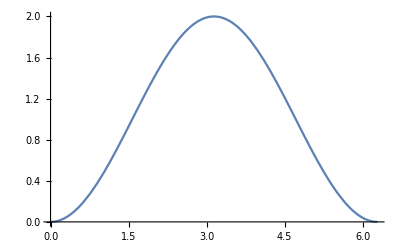

```mathematica
Plot[1-Cos[x],{x,0,2 π}]
```